# Assignment: 07

## On Linear regression

PH1050 Computational Physics

Aarya Gosar
EP23B025

Engineering Physics

12th Oct 2023

## Introduction

While analysing data, we often see two quantities being dependent on each other. In regression, we try to come up with a formula that predicts a quantity, given that we can measure the other quantity with certainity. In linear regression, we have a linear system of equations and we try to adjust the coefficient to match our data.

## Aim

1) Generate a linear data and try to get the best fit line using a) formula, b)Mathematica functions
2) Find best fit curve of a multi parameter system using a) mathematica functions b) Linear Algebra
3) Generate a non linear data and use the function NonLinearModelFit

## Code

### Linear Data

#### Generating the data

I have used the data from my highschool spring mass oscillator experiment
	X Axis : mass     Y Axis: T^2

{{100,1.21},{150,1.44},{200,2.11},{250,2.25},{300,2.56}}

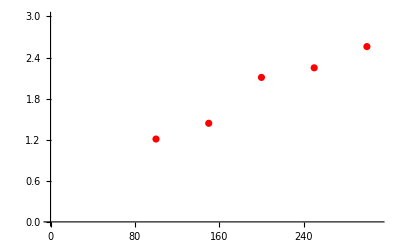

```mathematica
X = {100,150,200,250,300};
y = {1.21,1.44,2.11,2.25,2.56};
n = Length[X];
combinedData = Table[{X[[i]],y[[i]]},{i,1,n,1}]
pltPoints = ListPlot[combinedData,PlotRange->{{0,310},{0,3}}, PlotStyle->{Red,Thick}]
```

#### Best fit Line using Formula

M =

0.00702

C =

0.51

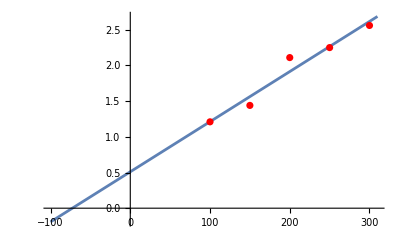

```mathematica
XiYi = Table[{X[[i]] * y[[i]]} , {i,1,n,1}];
Xi2 = Table[{X[[i]]^2} , {i,1,n,1}];
m = (n* Total[XiYi] - Total[X]*Total[y])/(n * (Total[Xi2])- Total[X]^2);
Print["M = "]
m = m[[1]]
c = (Total[y]*Total[Xi2] - Total[X]*Total[XiYi])/(n * (Total[Xi2])- Total[X]^2);
Print["C = "]
c = c[[1]]
datatest = Table[{x , m * x + c}, {x,-100,310}];
pltLine = ListLinePlot[datatest];
Show[pltLine,pltPoints]
```

We can see that it cuts X - Axis at ~ -75 which is mass of hanger.
which was actually the case when I did the experiment

#### Using Linear Model fit

FittedModel[0.51+0.00702 x]

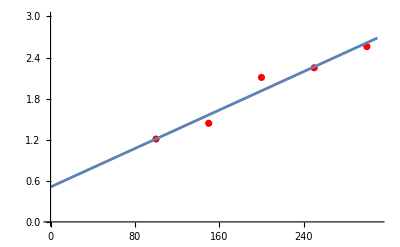

```mathematica
LineFormula = LinearModelFit[combinedData,{x,1} , x]
pltFormula = ListLinePlot[Table[{x , LineFormula[x]}, {x,0,310,1}]];
Show[pltPoints,pltFormula]
```

We Get the same result as before

### Multi Parameter

#### Generating data

This is experiment is from Newton’s law of cooling. Here we compare the temperature with time
X Axis: Time       Y Axis: θ

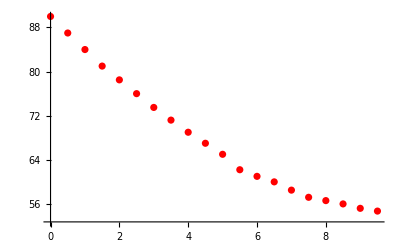

```mathematica
Clear["Global`*"]
θ = {90,87,84,81,78.5,76,73.5,71.2,69,67,65,62.2,61,60,58.5,57.2,56.6,56,55.2,54.7};
t = Table[time,{time,0,9.5,0.5}];
combinedData = Table[{ t[[i]], θ[[i]]} , {i,1,20,1}];
pltPoints = ListPlot[combinedData,PlotStyle->{Red,Thick}]
```

#### Making the curve using FindFit function

I have chosen the function:
 a3+a2 ⅇ^-x+a1/(1+x)

{a1→166.113,a2→-110.175,a3→38.2371}

38.2371-110.175 ⅇ^-x+166.113/(1+x)

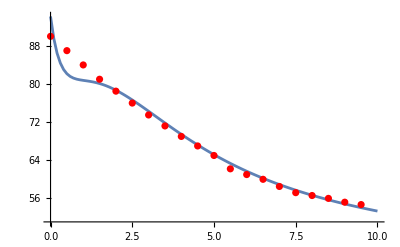

```mathematica
params = FindFit[combinedData,a1/(x+1)  + a2 Exp[-x] + a3 , {a1,a2,a3} , x]
FitCurve[x_] = a1/(x+1)  + a2 Exp[-x] + a3 /. params
pltCurve = ListLinePlot[Table[{x,FitCurve[x]} , {x,0,10,0.1}]];
Show[pltCurve,pltPoints]
```

#### Making the curve with Linear algebra

{166.113,-110.175,38.2371}

The function is same as above

38.2371-110.175 ⅇ^-x+166.113/(1+x)

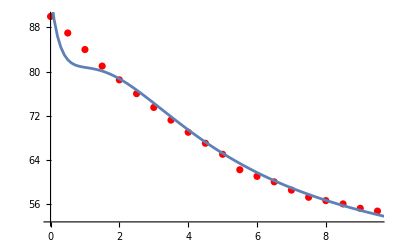

```mathematica
paramMatrix = Table[{1/(t[[i]]+1),  Exp[-t[[i]]] , 1} , {i,1,20,1}];
{a1,a2,a3} = LinearSolve[Transpose[paramMatrix].paramMatrix , Transpose[paramMatrix].θ]
Print["The function is same as above"]
LinearFitCurve[x_] = a1/(x+1) + a2 Exp[-x] + a3
pltCurveLinear = ListLinePlot[Table[{x,LinearFitCurve[x]} , {x,0,10,0.1}]];
Show[pltPoints,pltCurveLinear]
```

### Non Linear fit

#### Generating data

Here I will take data from PH1030 experiment on transistor characteristics
The Ic vs Vce graph is non linear as we require

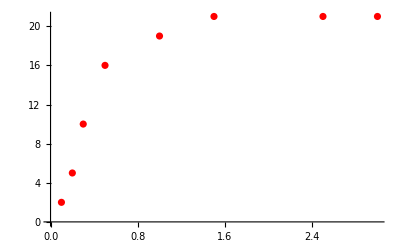

```mathematica
Clear["Global`*"]
X = {0.1,0.2,0.3,0.5,1,1.5,2.5,3};
y = {2,5,10,16,19,21,21,21};
combined = Table[{X[[i]] , y[[i]]} , {i,1,8,1}];
pltPoints = ListPlot[combined, PlotStyle->{Red,Thick,Bold}]
```

#### NonLinear function

The function I have chose is 
b ⅇ^(-c x)+a Log[x]+e Sin[d x]

FittedModel[19.2895 ⅇ^(-0.0972941 x)+7.93789 Log[x]+2.02666 Sin[1.64462 x]]

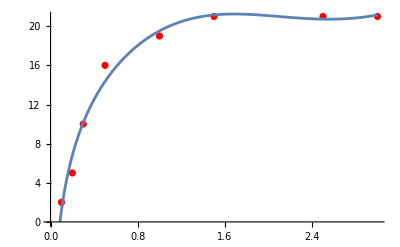

```mathematica
NonLinearFunc =NonlinearModelFit[combined,a Log[x] + b Exp[- c x] + e Sin[d x], {a,b,c,d,e} , x]
pltNonLinear = ListLinePlot[Table[{x,NonLinearFunc[x]},{x,0,3,0.01}]];
Show[pltPoints,pltNonLinear]
```

## Conclusion

As we can see, data from experiment is never precise. Regression helps us to find the correlation between two quantities subject to noise.
For simple systems we may choose to derive the equations ourselves or for complex systems we may use builtin functions of mathematica. We can see that the results are same irrespective of methods we choose.